```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
ig[r]
```

{{1/(1+z'[r]^2),0},{0,1/r^2}}

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
Cross[e[1][{r,θ}],e[2][{r,θ}]].Cross[e[1][{r,θ}],e[2][{r,θ}]]//FullSimplify
```

r^2 (1+z'[r]^2)

```mathematica
n[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
n[{r,θ}]
```

{-(Cos[θ] z'[r])/(√(1+z'[r]^2)),-(Sin[θ] z'[r])/(√(1+z'[r]^2)),1/(√(1+z'[r]^2))}

```mathematica
Derivative[ϵ[1]][e[1]][{r,θ}].n[{r,θ}]//FullSimplify
```

z''[r]/(√(1+z'[r]^2))

```mathematica
Derivative[ϵ[1]][e[2]][{r,θ}].n[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[1]][{r,θ}].n[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[2]][{r,θ}].n[{r,θ}]//FullSimplify
```

(r z'[r])/(√(1+z'[r]^2))

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].n[{r,θ}],Derivative[ϵ[1]][e[2]][{r,θ}].n[{r,θ}]},{Derivative[ϵ[2]][e[1]][{r,θ}].n[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].n[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in - \Nabla_{LB} H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
FullSimplify[ϕ'[r],Assumptions->ass]
```

1/(2 r^2 (1+z'[r]^2)^4)(3 z'[r]^5+z'[r]^7-r z''[r]+r z'[r]^6 z''[r]+z'[r] (1-r^2 z''[r] (7 z''[r]+10 r z^(3)[r]))+z'[r]^3 (3-r^2 z''[r] (7 z''[r]+10 r z^(3)[r]))+r^2 (-3 r z''[r]^3+2 z^(3)[r]+r z^(4)[r])+r z'[r]^4 (z''[r]+r (2 z^(3)[r]+r z^(4)[r]))+r z'[r]^2 (-z''[r]+15 r^2 z''[r]^3+2 r (2 z^(3)[r]+r z^(4)[r])))

```mathematica
(*sign*)
```

```mathematica
eq=FullSimplify[{κ(-1/sqrtdetg[r]ϕ'[r]-2H[r](H[r]^2-K[r]))+σ H[r]==0},Assumptions->ass]
```

```mathematica
κ=1;
σ=1;
Rmin=1;
Rmax=2;
CC=0.5;
```

```mathematica
bcs={z[Rmin]==CC,z'[Rmin]==CC,z[Rmax]==2 CC,z'[Rmax]==0};
```

```mathematica
s=NDSolve[Flatten[{eq,bcs}],z,{r,Rmin,Rmax}]
```

{{z→InterpolatingFunction[…]}}

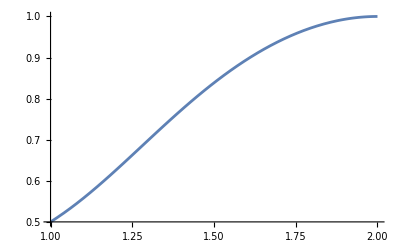

```mathematica
plotex=Plot[Evaluate[z[r]/. s],{r,Rmin,Rmax},PlotRange->All]
```

```mathematica
t=Import["~/Desktop/z.csv"];
t=Table[{Sqrt[t[[i,2]]^2+t[[i,3]]^2],t[[i,1]]},{i,1,Length[t]}]
```

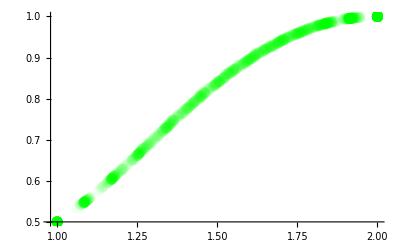

```mathematica
plotnum=ListPlot[t,PlotStyle->{Green,PointSize->0.02, Opacity->0.05},PlotRange->{CC,2 CC}]
```

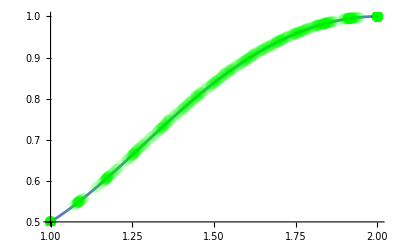

```mathematica
Show[plotex,plotnum]
```

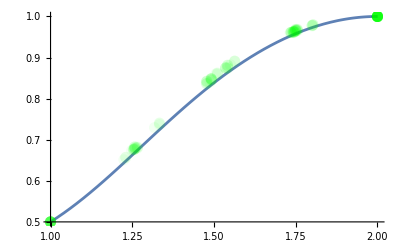

```mathematica
(*r=0.1*)
```

```mathematica
(*r=0.05*)
```